```mathematica
SetDirectory [NotebookDirectory[]];
(*En el programa sólo hay una fuente puntual orienta a lo largo del eje z en el extremo izquierdo de la silumación (aproximadamente x=-5 μm). Los pulsos se propagan en el vacío hasta la posición x=0μm. A partir de esta posición comienza el medio no lineal dispersivo,donde la contribución no lineal a la polarización en y (pyNLt3) se obtiene a partir de la polarización en z para el tiempo justo anterior (pzt2[mm]) y de la polarización en y para el tiempo actual (pyt3[mm]). La ecuación correspondiente en el programa es: 
pyNLt3[mm]=factorey*((pyt3[mm]+pzt2[mm])/2)*((pyt3[mm]+pzt2[mm])/2)
Análogamente se realiza para la componente perpendicular: pzNLt3.
De esta manera conseguimos que aunque al principio no teníamos campo eléctrico en y, al propagarse por el medio no lineal dispersivo se vaya generando este campo electrico Ey y campo magnético Hz. Luego este pulso generado se propaga siendo las ecuaciones del resto del código de manera análoga a los pulsos estudiados anteriormente. *)

deltatime=Import["Enodos1.txt",{"Data",1,1}]*10^-15;(*s*)
c=3*10^8; (*m/s*)
deltaSpace=deltatime*c;
size=Import["Enodos1.txt",{"Data",2,1}];
wall=Import["Enodos1.txt",{"Data",3,1}];
posdiscontinuidad=0;
```

```mathematica
campoEnodos1y=Import["Enodos1.txt",{"Data",Range[4,size+3],2}];
campoEnodos1z=Import["Enodos1.txt",{"Data",Range[4,size+3],3}];
datos3DEyt1=Table[{(-wall+i)*deltaSpace*10^6,campoEnodos1y[[i]],0},{i,1,size}];
datos3DEzt1=Table[{(-wall+i)*deltaSpace*10^6,0,campoEnodos1z[[i]]},{i,1,size}];
ListPointPlot3D[{datos3DEyt1,datos3DEzt1},PlotRange ->{All,{-1,1}, {-1,1}},PlotStyle-> {RGBColor[0,0,1],RGBColor[1,0,0]},  Axes->True,AxesLabel->{Style["Distancia de propagación(μm)",Black,12],Style[" Amplitud E_y(arb. unit)",Black,12],Style["Amplitud E_z(arb. unit)",Black,12]},PlotLabel->Style["Representación 3D Foto 1",Blue,16],PlotLegends->{"E_y","E_z"}]
```

-Graphics3D-

```mathematica
campoEnodos2y=Import["Enodos2.txt",{"Data",Range[4,size+3],2}];
campoEnodos2z=Import["Enodos2.txt",{"Data",Range[4,size+3],3}];
datos3DEyt2=Table[{(-wall+i)*deltaSpace*10^6,campoEnodos2y[[i]],0},{i,1,size}];
datos3DEzt2=Table[{(-wall+i)*deltaSpace*10^6,0,campoEnodos2z[[i]]},{i,1,size}];
ListPointPlot3D[{datos3DEyt2,datos3DEzt2},PlotRange ->{All,{-1,1}, {-1,1}},PlotStyle-> {RGBColor[0,0,1],RGBColor[1,0,0]},  Axes->True,AxesLabel->{Style["Distancia de propagación (μm)",Black,12],Style[" Amplitud E_y(arb. unit)",Black,12],Style["Amplitud E_z(arb. unit)",Black,12]},PlotLabel->Style["Representación 3D Foto 2",Blue,16],PlotLegends->{"E_y","E_z"}]
```

-Graphics3D-

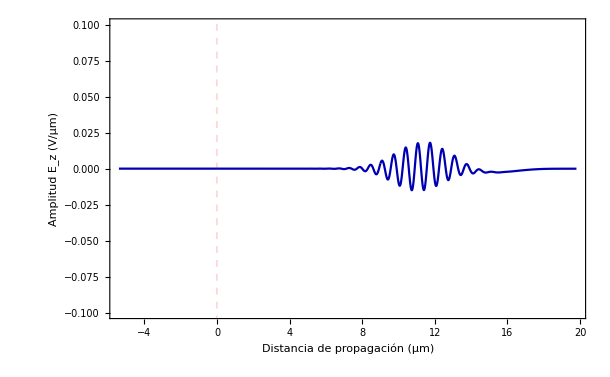

```mathematica
campoEnodos2y=Import["Enodos2.txt",{"Data",Range[4,size+3],2}];
datos2DEyt2=Table[{(-wall+i)*deltaSpace*10^6,campoEnodos2y[[i]]},{i,1,size}];
puntosEt2=ListPlot[datos2DEyt2,PlotStyle-> {PointSize[0.01],RGBColor[0,0,0.7]},PlotRange->{All,{-0.1,0.1}},Joined->True,Frame->True, FrameLabel->{"Distancia de propagación (μm)","Amplitud E_z (V/μm)"},FrameStyle->{Directive[Black,16],Directive[Black,16]},GridLines->{{{posdiscontinuidad,Directive[RGBColor[1,0,0],Dashed,Thick]}},None}, AxesOrigin->{100,0}]
```